Practical -3
                  3rd ORDER DIFFERENTIAL EQUATION

```mathematica
Q1 . y'''+2y'+y'=0
```

```mathematica
sol=DSolve[y'''[x]+2*y'[x]+y'[x]==0,y[x],x]
```

{{y[x]→C[3]-(C[2] Cos[√3 x])/(√3)+(C[1] Sin[√3 x])/(√3)}}

```mathematica
sol1=Evaluate[y[x]/.sol[[1]]/.{C[1]->1,C[2]->2,C[3]->3}]
```

3-(2 Cos[√3 x])/(√3)+Sin[√3 x]/(√3)

```mathematica
sol2=Evaluate[y[x]/.sol[[1]]/.{C[1]->0.5,C[2]->2,C[3]->3}]
```

3-(2 Cos[√3 x])/(√3)+0.288675 Sin[√3 x]

```mathematica
sol3=Evaluate[y[x]/.sol[[1]]/.{C[1]->-1,C[2]->-2,C[3]->0.5}]
```

0.5+(2 Cos[√3 x])/(√3)-Sin[√3 x]/(√3)

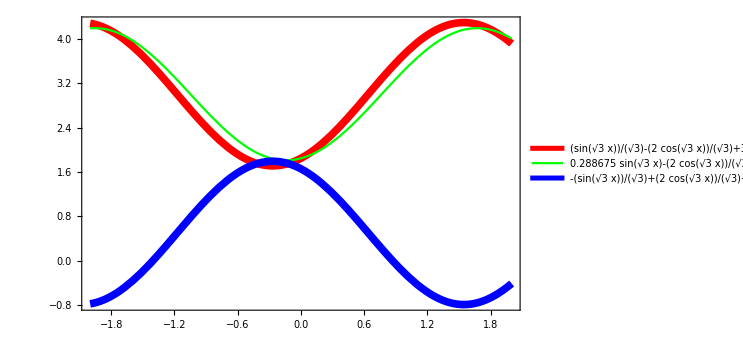

```mathematica
Plot[{sol1,sol2,sol3},{x,-2,2},PlotStyle->{{Red,Thickness[0.01]},{Green,Thick},{Blue,Thickness[0.01]}},PlotLegends->{sol1,sol2,sol3},Frame->True,
ImageSize->550]
```

```mathematica
Q2.y'''+y'=Tanx
```

```mathematica
sol=DSolve[y'''[x]+y'[x]==Tan[x],y[x],x]
```

{{y[x]→C[3]-C[2] Cos[x]-Log[Cos[x/2]-Sin[x/2]]-Log[Cos[x/2]+Sin[x/2]]+C[1] Sin[x]+Log[Cos[x/2]-Sin[x/2]] Sin[x]-Log[Cos[x/2]+Sin[x/2]] Sin[x]}}

```mathematica
sol1=Evaluate[y[x]/.sol[[1]]/.{C[1]->1,C[2]->2,C[3]->3}]
```

3-2 Cos[x]-Log[Cos[x/2]-Sin[x/2]]-Log[Cos[x/2]+Sin[x/2]]+Sin[x]+Log[Cos[x/2]-Sin[x/2]] Sin[x]-Log[Cos[x/2]+Sin[x/2]] Sin[x]

```mathematica
sol2=Evaluate[y[x]/.sol[[1]]/.{C[1]->-1,C[2]->-2,C[3]->1.3}]
```

1.3+2 Cos[x]-Log[Cos[x/2]-Sin[x/2]]-Log[Cos[x/2]+Sin[x/2]]-Sin[x]+Log[Cos[x/2]-Sin[x/2]] Sin[x]-Log[Cos[x/2]+Sin[x/2]] Sin[x]

```mathematica
sol3=Evaluate[y[x]/.sol[[1]]/.{C[1]->3/2,C[2]->0.5,C[3]->-2.5}]
```

-2.5-0.5 Cos[x]-Log[Cos[x/2]-Sin[x/2]]-Log[Cos[x/2]+Sin[x/2]]+(3 Sin[x])/2+Log[Cos[x/2]-Sin[x/2]] Sin[x]-Log[Cos[x/2]+Sin[x/2]] Sin[x]

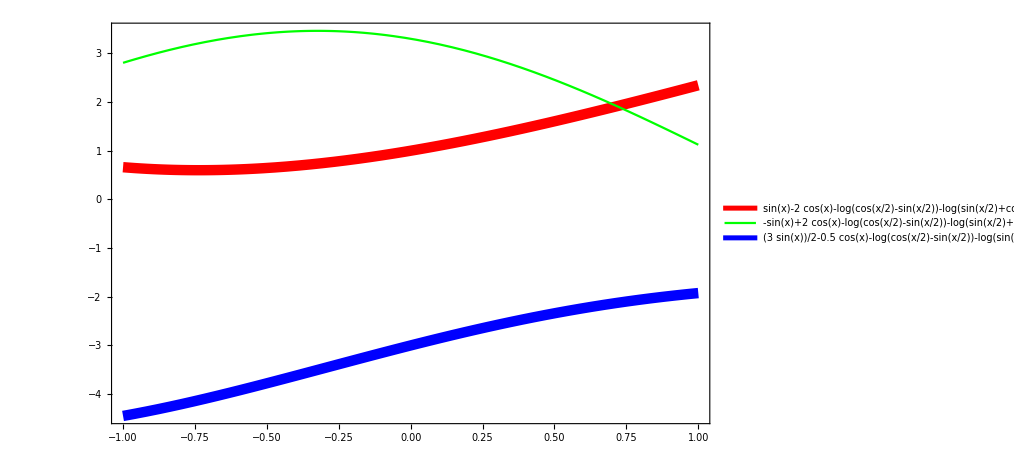

```mathematica
Plot[{sol1,sol2,sol3},{x,-1,1},PlotStyle->{{Red,Thickness[0.01]},{Green,Thick},{Blue,Thickness[0.01]}},PlotLegends->{sol1,sol2,sol3},Frame->True, ImageSize->750]
```

```mathematica
Q3.y'''+y'=0
```

```mathematica
sol=DSolve[y'''[x]+y'[x]==0,y[x],x]
```

{{y[x]→C[3]-C[2] Cos[x]+C[1] Sin[x]}}

```mathematica
sol1=Evaluate[y[x]/.sol[[1]]/.{C[1]->1,C[2]->2,C[3]->2/3}]
```

2/3-2 Cos[x]+Sin[x]

```mathematica
sol2=Evaluate[y[x]/.sol[[1]]/.{C[1]->0.5,C[2]->2,C[3]->3}]
```

3-2 Cos[x]+0.5 Sin[x]

```mathematica
sol3=Evaluate[y[x]/.sol[[1]]/.{C[1]->-1,C[2]->-2,C[3]->0.6}]
```

0.6+2 Cos[x]-Sin[x]

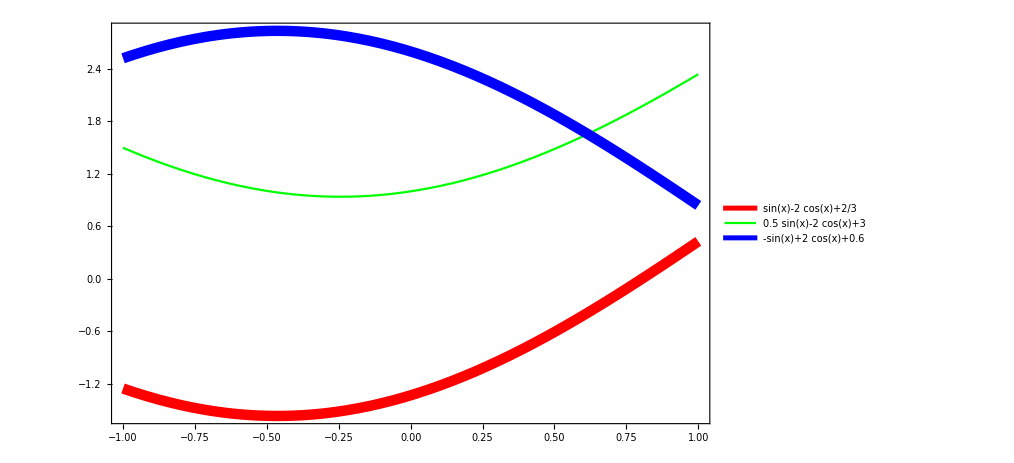

```mathematica
Plot[{sol1,sol2,sol3},{x,-1,1},PlotStyle->{{Red,Thickness[0.01]},{Green,Thick},{Blue,Thickness[0.01]}},PlotLegends->{sol1,sol2,sol3},Frame->True, ImageSize->750]
```

```mathematica
Q4.y'''-y''+100y'-100y=0,y(0)=4,y'(0)=11,y''(0)=-299
```

```mathematica
sol=DSolve[{y'''[x]-y''[x]+100*y'[x]-100*y[x]==0,y[0]==4,y'[0]==11,y''[0]==-299},y[x],x]
```

{{y[x]→ⅇ^x+3 Cos[10 x]+Sin[10 x]}}

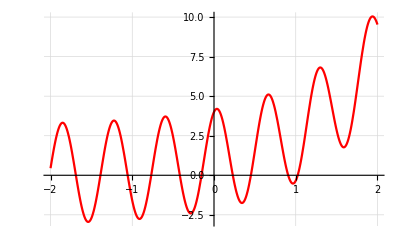

```mathematica
Plot[y[x]/.sol,{x,-2,2},PlotStyle->{Red},GridLines->Automatic]
```

```mathematica
Q5.y'''=x
```

```mathematica
sol=DSolve[y'''[x]==x,y[x],x]
```

{{y[x]→x^4/24+C[1]+x C[2]+x^2 C[3]}}

```mathematica
sol1=Evaluate[y[x]/.sol[[1]]/.{C[1]->1,C[2]->2,C[3]->3}]
```

1+2 x+3 x^2+x^4/24

```mathematica
sol2=Evaluate[y[x]/.sol[[1]]/.{C[1]->-1,C[2]->3,C[3]->2.7}]
```

-1+3 x+2.7 x^2+x^4/24

```mathematica
sol3=Evaluate[y[x]/.sol[[1]]/.{C[1]->3/4,C[2]->0.5,C[3]->-2.5}]
```

3/4+0.5 x-2.5 x^2+x^4/24

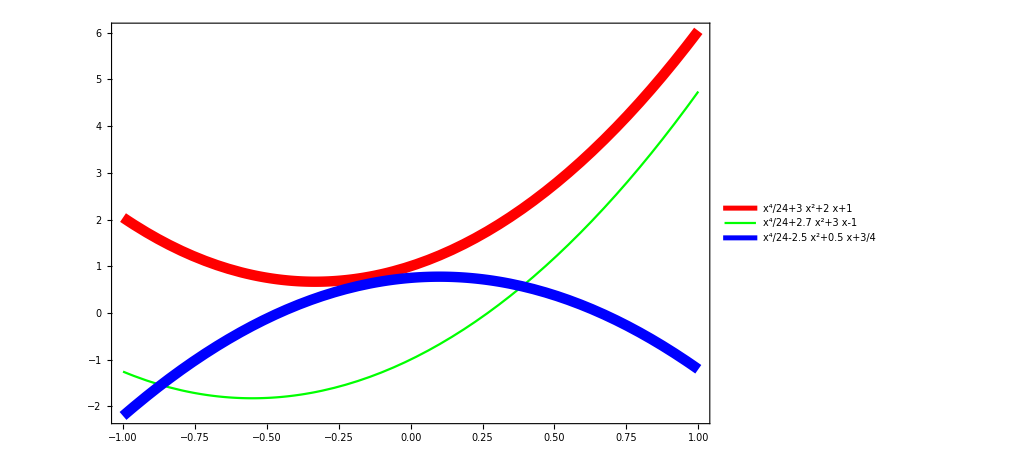

```mathematica
Plot[{sol1,sol2,sol3},{x,-1,1},PlotStyle->{{Red,Thickness[0.01]},{Green,Thick},{Blue,Thickness[0.01]}},PlotLegends->{sol1,sol2,sol3},Frame->True, ImageSize->750]
```

```mathematica
Q6.y'''+4y'=sec(2x)
```

```mathematica
sol=DSolve[y'''[x]+4*y'[x]==Sec[2x],y[x],x]
```

{{y[x]→C[3]-C[2] Cos[x]^2-1/4 x Cos[2 x]-1/8 Log[Cos[x]-Sin[x]]+1/8 Log[Cos[x]+Sin[x]]+1/2 C[1] Sin[2 x]+1/8 Log[Cos[2 x]] Sin[2 x]}}

```mathematica
sol1=Evaluate[y[x]/.sol[[1]]/.{C[1]->1,C[2]->2,C[3]->3}]
```

3-2 Cos[x]^2-1/4 x Cos[2 x]-1/8 Log[Cos[x]-Sin[x]]+1/8 Log[Cos[x]+Sin[x]]+1/2 Sin[2 x]+1/8 Log[Cos[2 x]] Sin[2 x]

```mathematica
sol2=Evaluate[y[x]/.sol[[1]]/.{C[1]->2.5,C[2]->1.5,C[3]->-3}]
```

-3-1.5 Cos[x]^2-1/4 x Cos[2 x]-1/8 Log[Cos[x]-Sin[x]]+1/8 Log[Cos[x]+Sin[x]]+1.25 Sin[2 x]+1/8 Log[Cos[2 x]] Sin[2 x]

```mathematica
sol3=Evaluate[y[x]/.sol[[1]]/.{C[1]->2/5,C[2]->-2,C[3]->3}]
```

3+2 Cos[x]^2-1/4 x Cos[2 x]-1/8 Log[Cos[x]-Sin[x]]+1/8 Log[Cos[x]+Sin[x]]+1/5 Sin[2 x]+1/8 Log[Cos[2 x]] Sin[2 x]

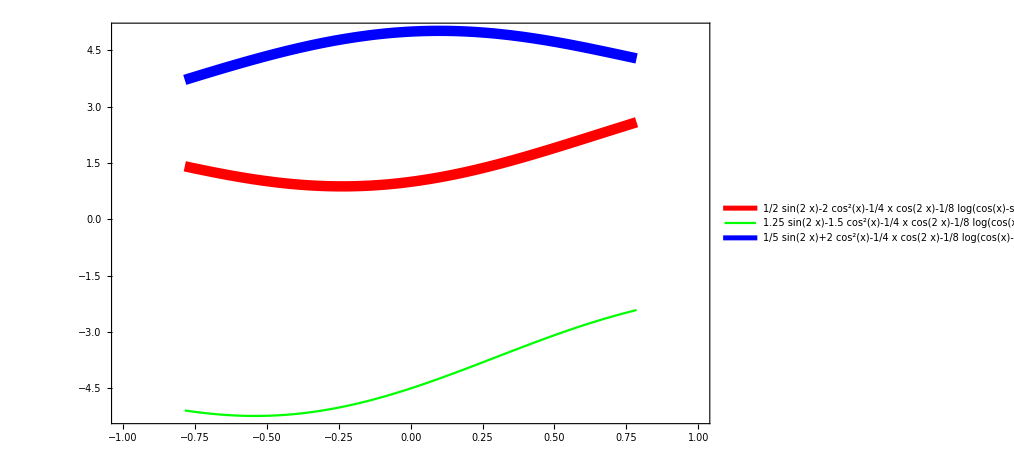

```mathematica
Plot[{sol1,sol2,sol3},{x,-1,1},PlotStyle->{{Red,Thickness[0.01]},{Green,Thick},{Blue,Thickness[0.01]}},PlotLegends->{sol1,sol2,sol3},Frame->True, ImageSize->750]
```

```mathematica
Q7.y'''-2y'-y'+2y=e^4x
```

```mathematica
sol=DSolve[y'''[x]-3*y'[x]+2*y[x]==Exp[4*x],y[x],x]
```

{{y[x]→ⅇ^(4 x)/54+ⅇ^(-2 x) C[1]+ⅇ^x C[2]+ⅇ^x x C[3]}}

```mathematica
sol1=Evaluate[y[x]/.sol[[1]]/.{C[1]->1,C[2]->2,C[3]->3}]
```

ⅇ^(-2 x)+2 ⅇ^x+ⅇ^(4 x)/54+3 ⅇ^x x

```mathematica
sol2=Evaluate[y[x]/.sol[[1]]/.{C[1]->5,C[2]->2,C[3]->-1}]
```

5 ⅇ^(-2 x)+2 ⅇ^x+ⅇ^(4 x)/54-ⅇ^x x

```mathematica
sol3=Evaluate[y[x]/.sol[[1]]/.{C[1]->-1,C[2]->2/3,C[3]->0.5}]
```

-ⅇ^(-2 x)+(2 ⅇ^x)/3+ⅇ^(4 x)/54+0.5 ⅇ^x x

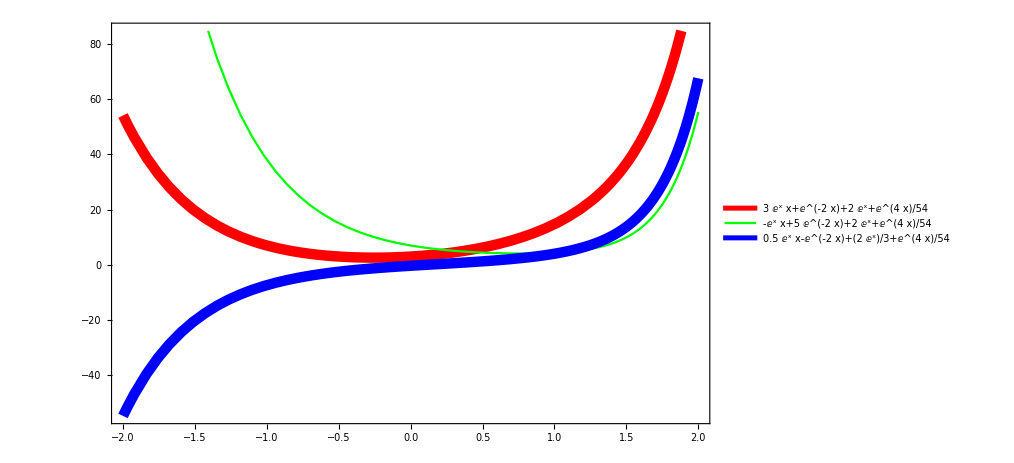

```mathematica
Plot[{sol1,sol2,sol3},{x,-2,2},PlotStyle->{{Red,Thickness[0.01]},{Green,Thick},{Blue,Thickness[0.01]}},PlotLegends->{sol1,sol2,sol3},Frame->True, ImageSize->750]
```